This workbook reads and exports NOS observed time/elevation datasets for a given list of stations, and also compares them to modeled results from ADCIRC.

# Read Station Locations

```mathematica
(*Read 15 for station locations*)

storm="floyd" (*"irene" or "floyd"*)
stepname="hurricane" (*"spindown" or "hurricane" or "spinup"*)

If[storm=="april2003_riverless",
r=StringJoin["D:\\Dropbox\\april2003\\riverless results\\"];
];

If[storm=="floyd",
r=StringJoin["D:\\Dropbox\\floyd\\",stepname,"\\"];
];

If[storm=="irene",
r=StringJoin["D:\\Dropbox\\irene\\",stepname,"\\"];
];

If[storm=="isabel",
r=StringJoin["D:\\Dropbox\\isabel\\",stepname,"\\"];
];

fpath15=StringJoin[r,"fort.15"];

s15=OpenRead[fpath15];
raw=ReadList[s15,String];

Close[s15];
"Use this scroll bar to find the line # of first + last stations ('start' & 'end')"
Manipulate[raw[[i]],{i,1,Length[raw],1}]
```

floyd

hurricane

Use this scroll bar to find the line # of first + last stations ('start' & 'end')

# Set Initialization Values

```mathematica
DayCount["March 15, 2003","May 15, 2003"]
```

61

```mathematica
(*start & end of the station list. Assumes the station locations are the same for 61 and 62*)
If[storm=="april2003"∨storm=="april2003_riverless",
stepname="spinup"];

If[stepname=="spinup"∨stepname=="spindown",
start=906; (*start line of the stations*)
end=3583; (*end line of the stations*)
,
start=907;end=3584;
];


xsecstart=142; (*of the stations, the number of the first of the boundary of interest.*)
xsecend=191; (*of the stations, the number of the end of the boundary of interest. *)
sitename="NOS_Stations";

(*april2003*)
If[storm=="april2003"∨storm=="april2003_riverless",
startyear=2003;
startmonth=3;
startdate=15;
rundays=60;
endyear=2003;
endmonth=5;
enddate=14;
];

(*floyd*)

If[storm=="floyd",
If[stepname=="spinup",
startyear=1999;
startmonth=8;
startdate=11;
rundays=31;
];
If[stepname=="spindown",
startyear=1999;
startmonth=9;
startdate=17;
rundays=30;
];
If[stepname=="hurricane",
startyear=1999;
startmonth=9;
startdate=11;
rundays=6;
];

endyear=1999;
endmonth=10;
enddate=16;
]

If[storm=="irene",
If[stepname=="spinup",
startyear=2011;
startmonth=7;
startdate=6;
endyear=2011;
endmonth=8;
enddate=20;
rundays=45;
];
If[stepname=="spindown",
startyear=2011;
startmonth=8;
startdate=30;
endyear=2011;
endmonth=9;
enddate=29;
rundays=40;
];
If[stepname=="hurricane",
startyear=2011;
startmonth=8;
startdate=20;
endyear=2011;
endmonth=8;
enddate=30;
rundays=10;
];
];


If[storm=="isabel",
If[stepname=="spinup",
startyear=2003;
startmonth=7;
startdate=31;
endyear=2003;
endmonth=9;
enddate=14;
rundays=45;
starthr=0;
startmin=0;
startsec=0;
];
If[stepname=="spindown",
startyear=2003;
startmonth=9;
startdate=19;
endyear=2003;
endmonth=10;
enddate=29;
rundays=40;
starthr=11;
startmin=30;
startsec=0;
];
If[stepname=="hurricane",
startyear=2003;
startmonth=9;
startdate=14;
endyear=2003;
endmonth=9;
enddate=20;
rundays=10;
starthr=0;
startmin=0;
startsec=0;
];
];


bathypath="D:\\Dropbox\\ADCIRC\\Data reading - bathymetries\\stationBathy.txt";(*text file. one column. one value for each station*)
path61=StringJoin[r,"fort.61"]; (*61 to use*)
wseoutpath=StringJoin[r,sitename,"_wse_model_",stepname,".txt"];(*output path for each boundary node's water surface elevations.*)
observedWSEoutpath=StringJoin[r,sitename,"_wse_observed_",stepname,".txt"];
modelwsescatterpath=StringJoin[r,sitename,"_wse_model_scatter",stepname,".txt"];

path62=StringJoin[r,"fort.62"];
davoutpath=StringJoin[r,sitename,"_dav",stepname,".txt"];

stationlist={8410140,8411250,8413320,8418150,8443970,8447930,8449130,8459681,8510560,
8531680,8534720,8536110,8557380,8632200,8636580,8637624,8638863,8651370,8652587,8654400,
8656483,8658120,8658163,8659084,8659897,2084472,208114150,8661070,8665530,8670870,8720218,
8720587,8721604,8723214,8723970,8724580,8725110,8726724,8727520,8728690,8729210,8729840,
8747766,8760551,8761724,8770570,8771510,8772440,8775870,8779770};

xsecend-xsecstart+1==Length[stationlist]
```

True

```mathematica
Position[stationlist,8653365]
```

{}

# Read 61 (Water Surface Elevation)

```mathematica
(*see bypass, below.*)


nstations=end-start+1;
(*
n61header=908;
n61headerstations=start-n61header;
n62header=;
n62stationstart=;
n62header=;
*)
"i"
Dynamic[i]
"j"
Dynamic[j]
StringJoin["validation Table - should be list of station indexes, going from ",ToString[xsecstart]," (xsecstart) to ",ToString[xsecend]," (xsecend)"]
Dynamic[validateTable]

stationlat=Table[0,{nstations}];
stationlon=Table[0,{nstations}];

s15=OpenRead[fpath15];
Skip[s15,String,(start-1)];

Do[
stationlon[[i]]=Read[s15,Number];
stationlat[[i]]=Read[s15,Number];
Skip[s15,String];
,{i,1,nstations}];

t=Read[s15,String];
Close[s15];

(*Generate WSE timeseries at each station's points*)
s=OpenRead[path61];
temp=ReadList[s,String];
L=Length[temp];
Close[s];

(*import 61 timeseries for target x-section*)
totalstations=nstations;
timesteps=(L-2)/(totalstations+1);

xsecstations=xsecend-xsecstart+1;

ts=Table[Table[0,{timesteps}],{xsecstations}];	
validateTable=Table[0,{xsecstations}];

s=OpenRead[path61];
Skip[s,String,xsecstart+2];(* *)

Do[
Do[
validateTable[[i]]=Read[s,Number];
ts[[i,j]]=Read[s,Number];
,{i,1,xsecstations}];
Skip[s,String,totalstations+1-xsecstations];(*<-- Replace with the total number of stations - the number of stations before the target xsection *)
,{j,timesteps}];
Close[s];

Export[wseoutpath,{timesteps,ts}];
```

i

j

validation Table - should be list of station indexes, going from 142 (xsecstart) to 191 (xsecend)

```mathematica
(*get times*)
times=Table[0,{timesteps}];
s=OpenRead[path61];
Skip[s,String,2];
timestart=AbsoluteTime[{startyear,startmonth,startdate,starthr,startmin,startsec}];

Do[
times[[i]]=Read[s,Number];
Skip[s,Number];
Skip[s,String,totalstations];
,{i,timesteps}];
Close[s];


times=times+timestart;
```

```mathematica
(*Bypass above code*)
ts=Import[wseoutpath];
ts=ToExpression[ts];

Do[
ts[[i]]=Transpose[Table[{times,ts[[i]]}]];
,{i,1,Length[ts]}]
Export[modelwsescatterpath,ts];
```

# Collect relevant NOS data

```mathematica
ots=Table[NOSimportrange[stationlist[[i]],startyear,startmonth,startdate,endyear,endmonth,enddate],{i,1,Length[stationlist]}];
Export[observedWSEoutpath,ots];
(*Do loop to import each timeseries*)
```

```mathematica
observedWSEoutpath
```

D:\Dropbox\floyd\hurricane\NOS_Stations_wse_observed_hurricane.txt

```mathematica
(*shortcut*)

(*unformatted import is failing. Let's be more intentional:*)
s=OpenRead[observedWSEoutpath];ots=ReadList[s,String];Close[s];

ots=StringJoin[ots];
(*Manipulate[
Show[
ListPlot[Transpose[Table[{tstimes,ts[[i]]}]],Joined->True,PlotRange->Full],
ListPlot[ots[[i]],PlotStyle->Black]
]
,{i,1,Length[ts],1}]*)
(*trim first and last "{}"*)





(*divide ots into station-specific data*)
otstemp=StringSplit[ots,"}}"];
ots=Table[0,{Length[otstemp]}];
Do[
ots[[i]]=ToExpression[StringJoin[otstemp[[i]],"}}"]];
,{i,1,Length[otstemp]}];
Clear[otstemp] (*ease memory creep*)
```

Thread::tdlen: Objects of unequal length in {}\ « 4 »\ {{3145996800, 1.035}, {3145997160, 1.034}, {3145997520, 1.056}, {3145997880, 1.051}, {3145998240, 1.043}, {3145998600, 1.042}, {3145998960, 1.046}, {3145999320, 1.044}, {3145999680, 1.046}, {3146000040, 1.057}, {3146000400, 1.051}, {3146000760, 1.044}, {3146001120, 1.016}, {3146001480, 1.01}, {3146001840, 0.985}, {3146002200, 0.948}, {3146002560, 0.924}, {3146002920, 0.904}, {3146003280, 0.887}, {3146003640, 0.872}, {3146004000, 0.855}, « 9 », {3146007600, 0.478}, {3146007960, 0.445}, {3146008320, 0.392}, {3146008680, 0.359}, {3146009040, 0.304}, {3146009400, 0.271}, {3146009760, 0.227}, {3146010120, 0.182}, {3146010480, 0.137}, {3146010840, 0.085}, {3146011200, 0.064}, {3146011560, 0.021}, {3146011920, -0.006}, {3146012280, -0.041}, {3146012640, -0.088}, {3146013000, -0.111}, {3146013360, -0.146}, {3146013720, -0.18}, {3146014080, -0.196}, {3146014440, -0.251}, « 8590 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {}\ {{3145996800, 1.035}, {3145997160, 1.034}, {3145997520, 1.056}, {3145997880, 1.051}, {3145998240, 1.043}, {3145998600, 1.042}, {3145998960, 1.046}, {3145999320, 1.044}, {3145999680, 1.046}, {3146000040, 1.057}, {3146000400, 1.051}, {3146000760, 1.044}, {3146001120, 1.016}, {3146001480, 1.01}, {3146001840, 0.985}, {3146002200, 0.948}, {3146002560, 0.924}, {3146002920, 0.904}, {3146003280, 0.887}, {3146003640, 0.872}, {3146004000, 0.855}, « 9 », {3146007600, 0.478}, {3146007960, 0.445}, {3146008320, 0.392}, {3146008680, 0.359}, {3146009040, 0.304}, {3146009400, 0.271}, {3146009760, 0.227}, {3146010120, 0.182}, {3146010480, 0.137}, {3146010840, 0.085}, {3146011200, 0.064}, {3146011560, 0.021}, {3146011920, -0.006}, {3146012280, -0.041}, {3146012640, -0.088}, {3146013000, -0.111}, {3146013360, -0.146}, {3146013720, -0.18}, {3146014080, -0.196}, {3146014440, -0.251}, « 8590 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {}\ {{3145996800, 0.834}, {3145997160, 0.875}, {3145997520, 0.908}, {3145997880, 0.925}, {3145998240, 0.964}, {3145998600, 0.989}, {3145998960, 1.015}, {3145999320, 1.038}, {3145999680, 1.025}, {3146000040, 1.058}, {3146000400, 1.083}, {3146000760, 1.084}, {3146001120, 1.103}, {3146001480, 1.103}, {3146001840, 1.1}, {3146002200, 1.097}, {3146002560, 1.112}, {3146002920, 1.129}, {3146003280, 1.137}, {3146003640, 1.13}, {3146004000, 1.127}, « 9 », {3146007600, 0.836}, {3146007960, 0.801}, {3146008320, 0.78}, {3146008680, 0.729}, {3146009040, 0.684}, {3146009400, 0.623}, {3146009760, 0.585}, {3146010120, 0.554}, {3146010480, 0.504}, {3146010840, 0.456}, {3146011200, 0.436}, {3146011560, 0.401}, {3146011920, 0.359}, {3146012280, 0.285}, {3146012640, 0.252}, {3146013000, 0.208}, {3146013360, 0.171}, {3146013720, 0.113}, {3146014080, 0.092}, {3146014440, 0.047}, « 6260 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

```mathematica
(*calculate NSE for each station*)
NSElist=Table[scatterNSinterp[ots[[i]],ts[[i]],"Hermite"][[1]],{i,1,Length[stationlist]}];
```

InterpolatingFunction::dmval: Input value {3271363200} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3271363560} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3271363920} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{}\ {{3271363200, -0.297}, {3271363560, -0.279}, {3271363920, -0.274}, {3271364280, -0.266}, {3271364640, -0.257}, {3271365000, -0.233}, {3271365360, -0.228}, {3271365720, -0.188}, « 35 », {3271378680, 0.281}, {3271379040, 0.312}, {3271379400, 0.304}, {3271379760, 0.294}, {3271380120, 0.303}, {3271380480, 0.308}, {3271380840, 0.302}, « 4750 »}] does not exist.

Thread::tdlen: Objects of unequal length in -{}\ {{3271363200, -0.297}, {3271363560, -0.279}, {3271363920, -0.274}, {3271364280, -0.266}, {3271364640, -0.257}, {3271365000, -0.233}, {3271365360, -0.228}, {3271365720, -0.188}, « 35 », {3271378680, 0.281}, {3271379040, 0.312}, {3271379400, 0.304}, {3271379760, 0.294}, {3271380120, 0.303}, {3271380480, 0.308}, {3271380840, 0.302}, « 4750 »} cannot be combined.

Part::partw: Part 2 of TagBox[InterpolatingFunction[{{3.2763747`*^9, 3.2768496`*^9}}, {5, 7, 0, {1584}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {Developer`PackedArrayForm, {« 1 »}, {0.079969939741`, 0.10574223712`, 0.1313676979`, 0.15674341916`, 0.1817591854`, 0.20629810839`, « 39 », 0.31765580038`, 0.29815857888`, 0.27943585082`, 0.26173660997`, 0.24466202451`, « 1534 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] does not exist.

Transpose::nmtx: The first two levels of « 1 » cannot be transposed.

Transpose::nmtx: The first two levels of {} {{3271363200, -0.297`}, {3271363560, -0.279`}, {3271363920, -0.274`}, {3271364280, -0.266`}, {3271364640, -0.257`}, {3271365000, -0.233`}, {3271365360, -0.228`}, {3271365720, -0.188`}, « 35 », {3271378680, 0.281`}, {3271379040, 0.312`}, {3271379400, 0.304`}, {3271379760, 0.294`}, {3271380120, 0.303`}, {3271380480, 0.308`}, {3271380840, 0.302`}, « 4750 »}TagBox[« 1 », False, Rule[Editable, False], Rule[SelectWithContents, True]][{} « 1 »] cannot be transposed.

Part::partw: Part 2 of Transpose[{}\ {{3271363200, 2.035}, {3271363560, 2.082}, {3271363920, 2.122}, {3271364280, 2.164}, {3271364640, ""}, {3271365000, ""}, {3271365360, ""}, {3271365720, ""}, « 35 », {3271378680, 2.636}, {3271379040, 2.603}, {3271379400, 2.593}, {3271379760, 2.585}, {3271380120, 2.562}, {3271380480, 2.536}, {3271380840, 2.509}, « 4719 »}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in -{}\ {{3271363200, 2.035}, {3271363560, 2.082}, {3271363920, 2.122}, {3271364280, 2.164}, {3271364640, ""}, {3271365000, ""}, {3271365360, ""}, {3271365720, ""}, {3271366080, ""}, « 33 », {3271378320, 2.667}, {3271378680, 2.636}, {3271379040, 2.603}, {3271379400, 2.593}, {3271379760, 2.585}, {3271380120, 2.562}, {3271380480, 2.536}, {3271380840, 2.509}, « 4719 »} cannot be combined.

Transpose::nmtx: The first two levels of {{}\ {{3271363200, 2.035}, {3271363560, 2.082}, {3271363920, 2.122}, {3271364280, 2.164}, {3271364640, ""}, {3271365000, ""}, {3271365360, ""}, {3271365720, ""}, {3271366080, ""}, « 34 », {3271378680, 2.636}, {3271379040, 2.603}, {3271379400, 2.593}, {3271379760, 2.585}, {3271380120, 2.562}, {3271380480, 2.536}, {3271380840, 2.509}, « 4719 »}, Transpose[« 1 »] ⟦ 2 ⟧} cannot be transposed.

General::stop: Further output of Transpose :: nmtx will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in -{}\ {{3271363200, -0.152}, {3271363560, -0.11}, {3271363920, -0.077}, {3271364280, -0.033}, {3271364640, 0.007}, {3271365000, 0.052}, {3271365360, 0.091}, {3271365720, 0.119}, « 35 », {3271378680, 0.523}, {3271379040, 0.486}, {3271379400, 0.455}, {3271379760, 0.432}, {3271380120, 0.404}, {3271380480, 0.369}, {3271380840, 0.344}, « 4750 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

```mathematica
ListPlot[NSElist]
```

Thread::tdlen: Objects of unequal length in {}\ {{3.2713632×10^9, -0.297}, {3.27136356×10^9, -0.279}, {3.27136392×10^9, -0.274}, {3.27136428×10^9, -0.266}, {3.27136464×10^9, -0.257}, {3.271365×10^9, -0.233}, « 39 », {3.2713794×10^9, 0.304}, {3.27137976×10^9, 0.294}, {3.27138012×10^9, 0.303}, {3.27138048×10^9, 0.308}, {3.27138084×10^9, 0.302}, « 4750 »} cannot be combined.

Part::partw: Part 2 of TagBox[InterpolatingFunction[{{3.2763747`*^9, 3.2768496`*^9}}, {5, 7, 0, {1584}, {4}, 0, 0, 0, 0, Automatic, {}, {}, False}, {{« 1 »}}, {Developer`PackedArrayForm, {« 1 »}, {0.079969939741`, 0.10574223712`, 0.1313676979`, 0.15674341916`, 0.1817591854`, 0.20629810839`, « 39 », 0.31765580038`, 0.29815857888`, 0.27943585082`, 0.26173660997`, 0.24466202451`, « 1534 »}}, {Automatic}], False, Rule[Editable, False], Rule[SelectWithContents, True]] does not exist.

Thread::tdlen: Objects of unequal length in -1.\ {}\ {{3.2713632×10^9, -0.297}, {3.27136356×10^9, -0.279}, {3.27136392×10^9, -0.274}, {3.27136428×10^9, -0.266}, {3.27136464×10^9, -0.257}, {3.271365×10^9, -0.233}, « 39 », {3.2713794×10^9, 0.304}, {3.27137976×10^9, 0.294}, {3.27138012×10^9, 0.303}, {3.27138048×10^9, 0.308}, {3.27138084×10^9, 0.302}, « 4750 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {}\ {{3.2713632×10^9, -0.297}, {3.27136356×10^9, -0.279}, {3.27136392×10^9, -0.274}, {3.27136428×10^9, -0.266}, {3.27136464×10^9, -0.257}, {3.271365×10^9, -0.233}, « 39 », {3.2713794×10^9, 0.304}, {3.27137976×10^9, 0.294}, {3.27138012×10^9, 0.303}, {3.27138048×10^9, 0.308}, {3.27138084×10^9, 0.302}, « 4750 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

Part::partw: Part 2 of Transpose[{}\ {{3.2713632×10^9, -0.297}, {3.27136356×10^9, -0.279}, {3.27136392×10^9, -0.274}, {3.27136428×10^9, -0.266}, {3.27136464×10^9, -0.257}, {3.271365×10^9, -0.233}, « 39 », {3.2713794×10^9, 0.304}, {3.27137976×10^9, 0.294}, {3.27138012×10^9, 0.303}, {3.27138048×10^9, 0.308}, {3.27138084×10^9, 0.302}, « 4750 »}] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

-Graphics-

23

Thread::tdlen: Objects of unequal length in {}\ {{3.2713632×10^9, -0.152}, {3.27136356×10^9, -0.11}, {3.27136392×10^9, -0.077}, {3.27136428×10^9, -0.033}, {3.27136464×10^9, 0.007}, {3.271365×10^9, 0.052}, « 39 », {3.2713794×10^9, 0.455}, {3.27137976×10^9, 0.432}, {3.27138012×10^9, 0.404}, {3.27138048×10^9, 0.369}, {3.27138084×10^9, 0.344}, « 4750 »} cannot be combined.

Thread::tdlen: Objects of unequal length in {}\ {{3.27136×10^9, -0.152}, {3.27136×10^9, -0.11}, {3.27136×10^9, -0.077}, {3.27136×10^9, -0.033}, {3.27136×10^9, 0.007}, {3.27137×10^9, 0.052}, {3.27137×10^9, 0.091}, « 37 », {3.27138×10^9, 0.486}, {3.27138×10^9, 0.455}, {3.27138×10^9, 0.432}, {3.27138×10^9, 0.404}, {3.27138×10^9, 0.369}, {3.27138×10^9, 0.344}, « 4750 »} cannot be combined.

ListPlot::lpn: {}\ {{3.27136×10^9, -0.152}, {3.27136×10^9, -0.11}, {3.27136×10^9, -0.077}, {3.27136×10^9, -0.033}, {3.27136×10^9, 0.007}, {3.27137×10^9, 0.052}, {3.27137×10^9, 0.091}, « 37 », {3.27138×10^9, 0.486}, {3.27138×10^9, 0.455}, {3.27138×10^9, 0.432}, {3.27138×10^9, 0.404}, {3.27138×10^9, 0.369}, {3.27138×10^9, 0.344}, « 4750 »} is not a list of numbers or pairs of numbers.

Thread::tdlen: Objects of unequal length in {}\ {{3.2713632×10^9, -0.152}, {3.27136356×10^9, -0.11}, {3.27136392×10^9, -0.077}, {3.27136428×10^9, -0.033}, {3.27136464×10^9, 0.007}, {3.271365×10^9, 0.052}, « 39 », {3.2713794×10^9, 0.455}, {3.27137976×10^9, 0.432}, {3.27138012×10^9, 0.404}, {3.27138048×10^9, 0.369}, {3.27138084×10^9, 0.344}, « 4750 »} cannot be combined.

General::stop: Further output of Thread :: tdlen will be suppressed during this calculation.

ListPlot::lpn: {}\ {{3.27136×10^9, -0.152}, {3.27136×10^9, -0.11}, {3.27136×10^9, -0.077}, {3.27136×10^9, -0.033}, {3.27136×10^9, 0.007}, {3.27137×10^9, 0.052}, {3.27137×10^9, 0.091}, « 37 », {3.27138×10^9, 0.486}, {3.27138×10^9, 0.455}, {3.27138×10^9, 0.432}, {3.27138×10^9, 0.404}, {3.27138×10^9, 0.369}, {3.27138×10^9, 0.344}, « 4750 »} is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in ListPlot[{} {{3271363200, -0.152`}, {3271363560, -0.11`}, {3271363920, -0.077`}, {3271364280, -0.033`}, {3271364640, 0.007`}, {3271365000, 0.052`}, {3271365360, 0.091`}, {3271365720, 0.119`}, « 36 », {3271379040, 0.486`}, {3271379400, 0.455`}, {3271379760, 0.432`}, {3271380120, 0.404`}, {3271380480, 0.369`}, {3271380840, 0.344`}, « 4750 »}, PlotStyle → InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

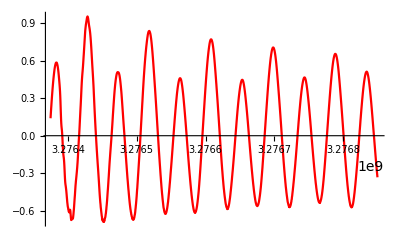
Show[ListPlot[{} {{3271363200,-0.152},{3271363560,-0.11},{3271363920,-0.077},{3271364280,-0.033},{3271364640,0.007},{3271365000,0.052},4788,{3273089040,0.035},{3273089400,0.003},{3273089760,-0.023},{3273090120,-0.049},{3273090480,-0.066},{3273090840,-0.083}},PlotStyle→GrayLevel[0]],-Graphics-]
 |  |  |  |

```mathematica
i=23

Show[ListPlot[ots[[i]],PlotStyle->Black],ListPlot[ts[[i]],Joined->True,PlotStyle->Red]]
```